## QSim` Documentation

### Preamble

QSim is a stand-alone package, and does not require other packages to run.

```mathematica
Needs["QSim`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["QuantumSystems`"]
Needs["Tensor`"]
Needs["Visualization`"]
Needs["GRAPE`"]
```

### Source Code

Open Source Code

## Introduction and Overview

QSim` is a general purpose quantum system time-evolution simulator whose primary objective is ease of use. This is in keeping with one of Mathematica’s main advantages over most other languages; rapid and intuitive development of ideas with minimal overhead. A description of the the quantum system, usually a Hamiltonian, and an action on that quantum system are provided, and some observable, quantum state, propogator, etc. is monitored as the system evolves.

As a quick example, the following computes the expectation value of X⊗Y of the initial state |00⟩ undergoing evolution with the time-dependent Hamiltonian H(t)=cos(t)X⊗X+sin(t)Y⊗Y. Note that over half the code is for plotting and not for simulating -- it is really a one liner!

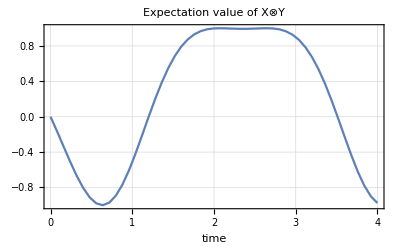

```mathematica
ListPlot[
Observables[PulseSim[Cos[#]TP[XX]+Sin[#]TP[XX]&,4,PollingInterval->0.1,InitialState->Projector[{1,0,0,0}],Observables->{TP[XY]}],TimeVector->True],
Joined->True,PlotRange->All,PlotTheme->"Detailed",
PlotLabel->"Expectation value of X⊗Y",FrameLabel->{"time",None}
]
```

## Simulation Output

The output of a simulation using PulseSim is determined by the option SimulationOutput. Usually the default value of Automatic will be sufficient.

SimulationOutput is a simulation option. Set this option to be one of, or a list of, the output types Unitaries, States, Functions, Observables, and Superoperators. The output type  TimeVector is always included. The default value is Automatic, described below. The output of a simulation has the form simulationOutput={Type1→data1,Type2→data2,...}. Data of a given type can generally be retrieved by using, for example, Type2[simulationOutput] which returns data2.

Note
Automatic output types returned by a given simulation are chosen using these rules:
| If no InitialState or Functions options are given, Unitaries is the only output type
| If InitialState is given as an option, but neither Observables nor Functions is, States is the only output type
| If InitialState is given as an option, and either of Observables or Functions is also, Observables or Functions will be the output type
| If Unitaries was supposed to be an automatic output type but the evolution was not pure (e.g. using LindbladForm) Superoperators will be the return type.

### TimeVector

TimeVector[simulationOutput] returns the TimeVector data from simulationOutput, as output by PulseSim. These data will be of the form {t1,t2,t3,...,tN} where t1=0 and tN is the total simulation time; the intermediate values are determined by the PollingInterval option.

Note
TimeVector is the only output type always returned by PulseSim.

### Unitaries

Unitaries[simulationOutput] returns the Unitaries data from simulationOutput, as output by PulseSim. These data will be of the form {U1,U2,U3,...,UN} where the n^th unitary matrix specifies to the total propagation up to the time specified by the n^th element of the TimeVector.

### States

States[simulationOutput] returns the States data from simulationOutput, as output by PulseSim.These data will be of the form {ρ1,ρ2,ρ3,...,ρN} where the n^th density matrix specifies the quantum state at the time specified by the n^th element of the TimeVector.

### Functions

Functions is a simulation option that specifies a list of functions {f_1,f_2,...,f_K} to evaluate during simulation. If an InitialState has been set, the functions are evaluated on the density matrix at each PollingInterval, otherwise, the functions are evaluated on the propagator (either unitary or superoperator) at each PollingInterval. The default value is None.

Functions[simulationOutput] returns the Functions data from simulationOutput, as output by PulseSim. These data will be of the form {fun1,fun2,..,funK} where funk is a list of the form funk={funk1,funk2,funk3,...,funkN}, where the n^th element corresponds to the k^th function’s value at the time specified by the n^th element of the TimeVector.

Functions[simulationOutput,TimeVector→True] returns the Functions data including time information from simulationOutput, as output by PulseSim. These data will be of the form {fun1,fun2,..,funK} where funk is of the form funk={{t1,funk1},{t2,funk2},...,{tN,funkN}}, a list of tuples of TimeVector values and function values.

Note
Functions[simulationOutput] always outputs in a format that is accepted by ListPlot, assuming the functions have plotable values (which need not be true).

### Observables

Observables is a simulation option that specifies a list of observables {A_1,A_2,...,A_K} (square matrices) to keep track of during simulation. Given an observable A, the observable value is computed as Tr(ρ.A) where ρ is the density matrix at a given time. The default value is None.

Observables[simulationOutput] returns the Observables data from simulationOutput, as output by PulseSim. These data will be of the form {obs1,obs2,..,obsK} where obsk is a list of the form obsk={obsk1,obsk2,obsk3,...,obskN}, where the n^th element corresponds to the k^th observable value at the time specified by the n^th element of the TimeVector.

Observables[simulationOutput,TimeVector→True] returns the Observables data including time information from simulationOutput, as output by PulseSim. These data will be of the form {obs1,obs2,..,obsK} where obsk is of the form obsk={{t1,obsk1},{t2,obsk2},...,{tN,obskN}}, a list of tuples of TimeVector values and observable values.

Note
Observables[simulationOutput] always outputs in a format that is accepted by ListPlot.

### Superoperators

Superoperators[simulationOutput] returns the Superopercators data from simulationOutput, as output by PulseSim. These data will be of the form {S1,S2,S3,...,SN} where the n^th superoperator specifies to the total super propagation up to the time specified by the n^th element of the TimeVector.

## PulseSim

PulseSim[H,pulse] simulates the pulse under the Hamiltonian H, which can be time independent, a square hermitian matrix, or time dependent, a function with a single argument that returns square hermitian matrices.

PulseSim[H,{p1,p2,p3,...}] evaluates the pulse sequence {p1,p2,p3,...} by evaluting each PulseSim[H,pi] and properly joining the results together. The pulse p1 is applied first, and then p2, etc. The initial state for one pulse is taken to be the final state of the previous pulse, likewise for propagators, etc.

PulseSim[H,pulse,distribution] evaluates PulseSim[H,pulse] for each member of the distribution and takes the expectation value over results. In the case of Unitaries, the expectation value is taken in superoperator space. The distribution should be formatted as {{prob1,prob2,...},{{symb1→val11,symb2→val12,...},{symb1→val21,symb2→val22,...},...}}, the same as ParameterDistribution from GRAPE`.

PulseSim[LindbladForm[H,{L1,L2,...,LK}],...] simulates the pulse or pulse sequence (with or without a distribution) under the Hamiltonian H with Lindblad dissipators L1,L2,...,LK. Any of the Lindblad dissipators can be time dependent or independent, as with the Hamiltonian.

Pulse Types
Pulses can be any of the following. See corresponding predicate functions for more details.
• Drift Pulse. Matched by predicate DriftPulseQ, a number or symbol representing evolution time under the given Hamiltonian.
• Shaped Pulse. Matched by predicate ShapedPulseQ, a tuple of control amplitudes and control Hamiltonians; {amps,{Hctl1,Hctl2,...}, where amps is a filename string or matrix of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt2,a21,a22,...},...}, where dti is the i^th time step length and aik is the amplitude of the k^th control Hamiltonian at the i^th step.
• Unitary Pulse. Matched by predicate UnitaryPulseQ, a tuple {U,t} where U is a unitary to apply and t is the time it is assigned to take.
• Channel Pulse. Matched by predicate ChannelPulseQ, a tuple {C,t} where C is a QuantumChannel and t is the time it is assigned to take.

Output
The output of a simulation has the form simulationOutput={Type1→data1,Type2→data2,...}. where the types can be any of TimeVector, Unitaries, States, Functions, Observables, and Superoperators. Data of a given type can generally be retrieved by using, for example, Type2[simulationOutput] which returns data2. See the option SimulationOutput and the documentation section Simulation Output for details.

Options
StepSize, PollingInterval, InitialState, Observables, Functions, SimulationOutput, NumericEvaluation, SequenceMode,ForceSuperoperator

### Options

#### StepSize

StepSize is a simulation option that chooses the time discretization when the internal Hamiltonian is time dependent. The default value is Automatic, which maximizes the norm of the internal Hamiltonian over the simulation period and uses a tenth of the inverse.

#### PollingInterval

PollingInterval is a simulation option that specifies the time interval at which results of the simulation should be returned. The default value is Off, where only values at time zero and final time returned. Each ouput type returns a value at each polling time. If used as an option with a pulse sequence, this option can be a list specifying a different polling interval for each pulse in the sequence.

Note
The PollingInterval does not affect the resolution at which the system is simulated, it only affects the interval at which an output is demanded; PollingInterval is completely unrelated to the StepSize of a time dependent Hamiltonian, or the pulse widths of a ShapedPulseQ. These times need not be even multiples of each other.

#### InitialState

InitialState is a simulation option that specifies the initial density matrix of the simulation. The default value is None where only propagators will be computed.

#### Observables

Observables is a simulation option that specifies a list of observables (square matrices) to keep track of during simulation. Given an observable A, the observable value is computed as Tr(ρ.A) where ρ is the density matrix at a given time. The default value is None.

See the section Observables for more information.

#### Functions

Functions is a simulation option that specifies a list of functions to evaluate during simulation. If an InitialState has been set, the functions are evaluated on the density matrix at each PollingInterval, otherwise, the functions are evaluated on the propagator (either unitary or superoperator) at each PollingInterval. The default value is None.

See the section Functions for more information.

#### SimulationOutput

SimulationOutput is a simulation option which should be one of, or a list of, the output types Unitaries, States, Functions, Observable, and Superoperators. 

See the full section Simulation Output for details.

#### NumericEvaluation

NumericEvaluation is a simulation option which, when set to True, N is explicitly called inside MatrixExp, and if set to False, N is not explicitly called. The default value is True.

#### SequenceMode

SequenceMode is a simulation option which when set to True, PulseSim returns the final state (or None) in addition to the usual output. This option is used internally to implement pulse sequences and should not be ordinarily be used otherwise.

#### ForceSuperoperator

ForceSuperoperator is a simulation option which forces output propagators to be in superoperator space, even if unitary space is sufficient. In this case, Functions which would normally act on unitaries instead act on superoperators. Note that all computations that can still be done in unitary space will still be done that way.

### Examples: Single Pulse

#### Basic Simulation

To run a simulation, specify a Hamiltonian and a pulse. Interpretting the output is discussed in the section Simulation Output.

```mathematica
H=Spin[X][1/2];
PulseSim[H,1]
```

{Unitaries→{{{1,0},{0,1}},{{0.877583+0. ⅈ,0.-0.479426 ⅈ},{0.-0.479426 ⅈ,0.877583+0. ⅈ}}},TimeVector→{0,1}}

#### Numeric vs Symbolic Computation

By default, the option NumericEvaluation is True:

```mathematica
PulseSim[Spin[X][1/2],1]
```

{Unitaries→{{{1,0},{0,1}},{{0.877583+0. ⅈ,0.-0.479426 ⅈ},{0.-0.479426 ⅈ,0.877583+0. ⅈ}}},TimeVector→{0,1}}

If set to False, PulseSim will atempt to solve the system symbolically. This will of course only succeed in a reasonable amount of time for simple systems.

```mathematica
PulseSim[Spin[X][1/2],t,NumericEvaluation->False]
```

{Unitaries→{{{1,0},{0,1}},{{Cos[t/2],-ⅈ Sin[t/2]},{-ⅈ Sin[t/2],Cos[t/2]}}},TimeVector→{0,t}}

#### Changing the Polling Interval

Our total simulation time is 5, and the polling interval is 1. We therefore expect output sampled at the times 0,1,2,3,4, and 5.

```mathematica
outputdata=PulseSim[TP[X],5,PollingInterval->1]
```

{Unitaries→{{{1,0},{0,1}},{{0.540302+0. ⅈ,0.-0.841471 ⅈ},{0.-0.841471 ⅈ,0.540302+0. ⅈ}},{{-0.416147+0. ⅈ,0.-0.909297 ⅈ},{0.-0.909297 ⅈ,-0.416147+0. ⅈ}},{{-0.989992+0. ⅈ,0.-0.14112 ⅈ},{0.-0.14112 ⅈ,-0.989992+0. ⅈ}},{{-0.653644+0. ⅈ,0.+0.756802 ⅈ},{0.+0.756802 ⅈ,-0.653644+0. ⅈ}},{{0.283662+0. ⅈ,0.+0.958924 ⅈ},{0.+0.958924 ⅈ,0.283662+0. ⅈ}}},TimeVector→{0,1,2,3,4,5}}

#### Tracking Observables

We compute the observables Y and Z as we rotate about the X axis, starting with the initial state |0⟩⟨0|. The observables are computed every 0.1 time units.

```mathematica
outputdata=PulseSim[TP[X],1,PollingInterval->0.1,InitialState->TP[U],Observables->{TP[Y],TP[Z]}]
```

{Observables→{{0,-0.198669,-0.389418,-0.564642,-0.717356,-0.841471,-0.932039,-0.98545,-0.999574,-0.973848,-0.909297},{1,0.980067,0.921061,0.825336,0.696707,0.540302,0.362358,0.169967,-0.0291995,-0.227202,-0.416147}},TimeVector→{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}}

Data can be collected with Observables.

{{0,-0.198669,-0.389418,-0.564642,-0.717356,-0.841471,-0.932039,-0.98545,-0.999574,-0.973848,-0.909297},{1,0.980067,0.921061,0.825336,0.696707,0.540302,0.362358,0.169967,-0.0291995,-0.227202,-0.416147}}

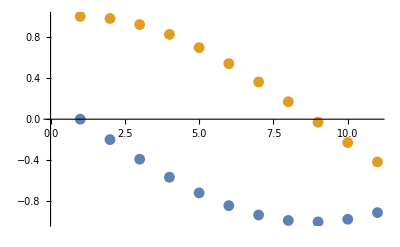

```mathematica
Observables[outputdata]
ListPlot[Observables[outputdata]]
```

Note that the TimeVector option adds corresponding times to the data:

{{{0,0},{1/10,-0.198669},{1/5,-0.389418},{3/10,-0.564642},{2/5,-0.717356},{1/2,-0.841471},{3/5,-0.932039},{7/10,-0.98545},{4/5,-0.999574},{9/10,-0.973848},{1,-0.909297}},{{0,1},{1/10,0.980067},{1/5,0.921061},{3/10,0.825336},{2/5,0.696707},{1/2,0.540302},{3/5,0.362358},{7/10,0.169967},{4/5,-0.0291995},{9/10,-0.227202},{1,-0.416147}}}

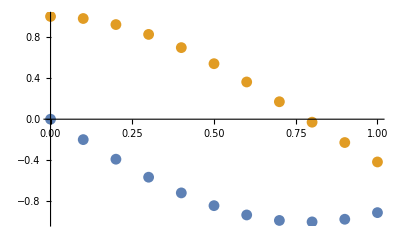

```mathematica
Observables[outputdata,TimeVector->True]
ListPlot[Observables[outputdata,TimeVector->True]]
```

#### Tracking Arbitrary Functions

We evolve the initial state |0⟩⟨0|⊗𝟙/2 under the Hamiltonian X⊗X+Y⊗Y+𝟙⊗X for 5 time units. We compute three functions; one that traces out the first subsystem, one that traces out the second subsystem, and one that takes the purity of the second subsystem.

```mathematica
outputdata=PulseSim[TP[XX+YY+IX],5,PollingInterval->0.05,InitialState->TP[UI]/2,
Functions->{
PartialTr[#,{2,2},{1}]&,
PartialTr[#,{2,2},{2}]&,
With[{ρ=PartialTr[#,{2,2},{1}]},Re@Tr[ρ.ρ]]&
}
];
```

Output Functions data can be collected with Functions. This consists of three lists, one list for each function.

```mathematica
Functions[outputdata]//Dimensions
```

{3,101}

Plot the purity of the second subsystem as a function of time:

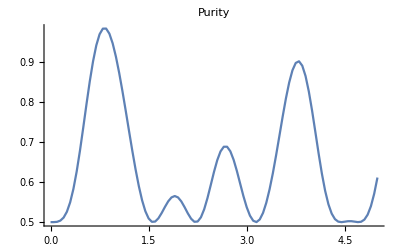

```mathematica
ListPlot[Last@Functions[outputdata,TimeVector->True],Joined->True,PlotLabel->"Purity"]
```

Plot the Bloch ball trajectories of the two subsystems.

```mathematica
BlochPlot[Functions[outputdata]⟦{1,2}⟧,BlochPlotJoined->True,BlochPlotLabels->{"Second Subsystem","First Subsystem"}]
```

-Graphics3D-

#### Tracking States

Track the initial state |0⟩⟨0| as it evolves about the X axis every 0.1 time units for 1 time unit.

```mathematica
outputdata=PulseSim[TP[X],1,PollingInterval->0.1,InitialState->TP[U]];
```

List the output states.

```mathematica
States[outputdata]//Chop//MatrixListForm
```

(1 | 0
0 | 0),(0.990033 | 0.+0.0993347 ⅈ
0.-0.0993347 ⅈ | 0.00996671),(0.96053 | 0.+0.194709 ⅈ
0.-0.194709 ⅈ | 0.0394695),(0.912668 | 0.+0.282321 ⅈ
0.-0.282321 ⅈ | 0.0873322),(0.848353 | 0.+0.358678 ⅈ
0.-0.358678 ⅈ | 0.151647),(0.770151 | 0.+0.420735 ⅈ
0.-0.420735 ⅈ | 0.229849),(0.681179 | 0.+0.46602 ⅈ
0.-0.46602 ⅈ | 0.318821),(0.584984 | 0.+0.492725 ⅈ
0.-0.492725 ⅈ | 0.415016),(0.4854 | 0.+0.499787 ⅈ
0.-0.499787 ⅈ | 0.5146),(0.386399 | 0.+0.486924 ⅈ
0.-0.486924 ⅈ | 0.613601),(0.291927 | 0.+0.454649 ⅈ
0.-0.454649 ⅈ | 0.708073)

Plot the output states on the Bloch sphere.

```mathematica
BlochPlot[States[outputdata],BlochPlotJoined->True]
```

-Graphics3D-

#### Simulating Shaped Pulses

Use RandomSmoothPulse from the GRAPE` package to generate a random pulse with 20 steps. The first column has time step lengths, the second and third columns are control Hamiltonian amplitudes.

{{0.1,-0.367948,-0.543174},{0.1,-0.742486,-0.377105},{0.1,-0.884121,-0.333492},{0.1,-0.841126,-0.380598},{0.1,-0.661772,-0.486684},{0.1,-0.394333,-0.620012},{0.1,-0.0870806,-0.748843},{0.1,0.211713,-0.84144},{0.1,0.453776,-0.866064},{0.1,0.590836,-0.790976},{0.1,0.57683,-0.586297},{0.1,0.416527,-0.264909},{0.1,0.165525,0.117547},{0.1,-0.118369,0.503571},{0.1,-0.377345,0.835663},{0.1,-0.553595,1.05632},{0.1,-0.589312,1.10805},{0.1,-0.426687,0.933336},{0.1,-0.00791209,0.474692},{0.1,0.724821,-0.325387}}

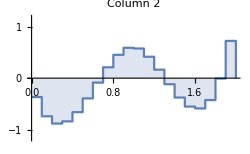
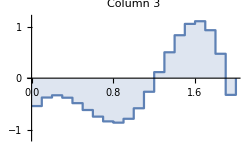

```mathematica
pulse=RandomSmoothPulse[0.1,20,{{-1,1},{-1,1}}]
PulsePlot[ToPulse@pulse,ImageSize->250,PlotLabel->DistributeOption["Column 2","Column 3"]]
```

What we plug into PulseSim as the pulse is {pulse,{controlHam1,controlHam2}}. View the trajectory of the initial state as this pulse is applied.

```mathematica
outputdata=PulseSim[TP[Z],{pulse,{TP[X],TP[Y]}},PollingInterval->0.05,InitialState->TP[U]];
BlochPlot[States[outputdata],BlochPlotJoined->True]
```

-Graphics3D-

#### Time Dependent Hamiltonians

Enter a Hamiltonian as a function of one argument, time.

```mathematica
Ht[t_]:=Cos[t]TP[XX]+Sin[t]TP[XX];
```

PulseSim simulates by discretizing the time domain. The step size of this discretization can be determined automatically, or explicitly set using StepSize. The step size is completely unrelated to the PollingInterval.

```mathematica
outputdata1=PulseSim[Ht,4,PollingInterval->0.1,InitialState->Projector[{1,0,0,0}],Observables->{TP[XY]}];
outputdata2=PulseSim[Ht,4,PollingInterval->0.1,InitialState->Projector[{1,0,0,0}],Observables->{TP[XY]},StepSize->0.01];
```

Plot the resulting data. The two computations lie on top of each other.

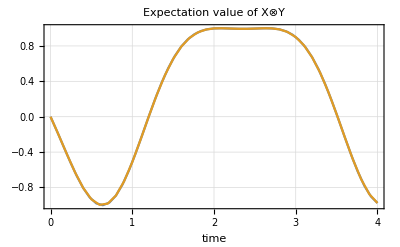

```mathematica
ListPlot[
Join[Observables[outputdata1,TimeVector->True],Observables[outputdata2,TimeVector->True]],
Joined->True,PlotRange->All,PlotTheme->"Detailed",
PlotLabel->"Expectation value of X⊗Y",FrameLabel->{"time",None}
]
```

#### Lindbladians

We use a Hamiltonian that evolves about a vector on the XZ plane, and we apply a  continuous depolarizing channel.

```mathematica
L=LindbladForm[2π 5 Spin[X][1/2]-2π 2 Spin[Z][1/2],{TP[Y],TP[X],TP[Z]}/Sqrt[2]];
```

Simulate this with some initial state. Also record the purity.

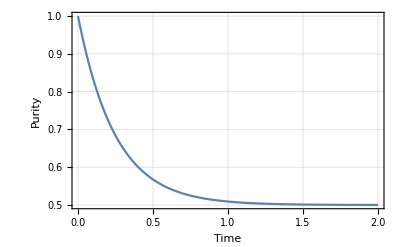

-Graphics3D-

```mathematica
outputdata=PulseSim[L,2,PollingInterval->0.01,InitialState->TP[U],Functions->{Tr[#.#]&},SimulationOutput->{States,Functions}];
ListPlot[Functions[outputdata,TimeVector->True],Joined->True,PlotTheme->"Detailed",FrameLabel->{"Time","Purity"},PlotRange->All]
BlochPlot[States[outputdata],BlochPlotJoined->True]
```

Similarly, we can also add time dependent Hamilonians and or Lindbladians.

```mathematica
L=LindbladForm[2π 5 Spin[X][1/2],{TP[Z]/Sqrt[2+Sin[4#]^2]&}];
```

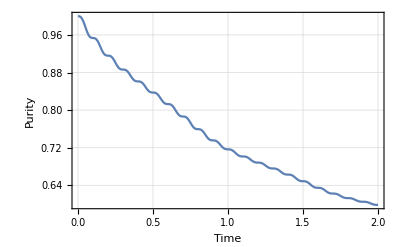

-Graphics3D-

```mathematica
outputdata=PulseSim[L,2,PollingInterval->0.01,StepSize->0.001,InitialState->TP[U],Functions->{Tr[#.#]&},SimulationOutput->{States,Functions}];
ListPlot[Functions[outputdata,TimeVector->True],Joined->True,PlotTheme->"Detailed",FrameLabel->{"Time","Purity"},PlotRange->All]
BlochPlot[States[outputdata],BlochPlotJoined->True]
```

### Examples: Pulse Sequences

#### Example 1

Define a sequence that begins and ends with a unitary pulse, with drift Hamiltonian evolution in between.

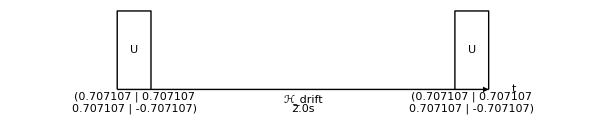

```mathematica
U=TP[H];
seq={{U,1},2,{U,0.5}};
DrawSequence@seq
```

Simulate and plot the observables. Note the effect of the application time of the unitary U.

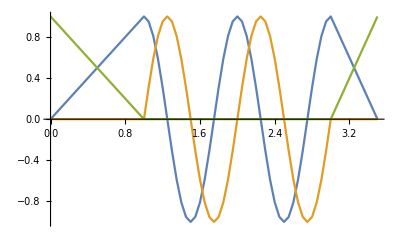

```mathematica
outputdata=PulseSim[2π Spin[Z][1/2],seq,InitialState->TP[U],PollingInterval->0.05,Observables->{TP[X],TP[Y],TP[Z]}];
ListPlot[Observables[outputdata,TimeVector->True],Joined->True,PlotRange->All]
```

#### Example 2

Define a sequence that begins and ends with a unitary pulse, with drift Hamiltonian evolution in between.

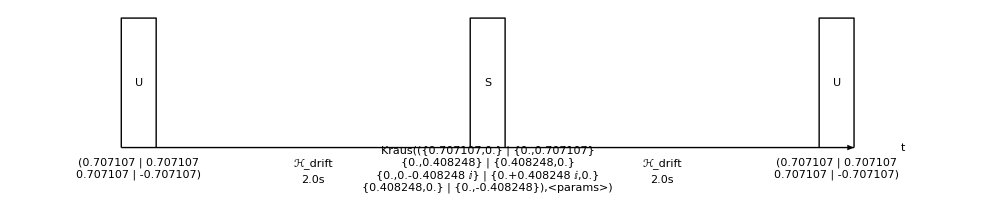

```mathematica
U=TP[H];
depolarizing=With[{p=0.5},Kraus[{Sqrt[1-p] Subscript[𝟙, 2],Sqrt[p/3]TP[X],Sqrt[p/3]TP[Y],Sqrt[p/3]TP[Z]}]];
seq={{U,1},2,{depolarizing,.2},2,{U,1}};
DrawSequence@seq
```

Simulate and plot the observables. Note the effect of the application time of the unitary U.

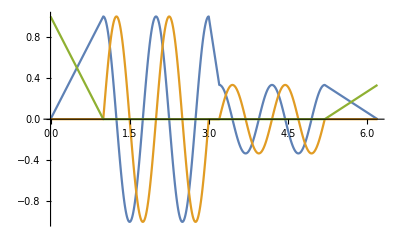

-Graphics3D-

```mathematica
outputdata=PulseSim[2π Spin[Z][1/2],seq,InitialState->TP[U],PollingInterval->0.01,Observables->{TP[X],TP[Y],TP[Z]},SimulationOutput->{Observables,States}];
ListPlot[Observables[outputdata,TimeVector->True],Joined->True,PlotRange->All]
BlochPlot[States@outputdata,BlochPlotJoined->True,InterpolationOrder->1]
```

### Examples: Parameter Distributions

### Implementation Details

All simulation is implemented using time slicing and the MatrixExp function.

## Auxiliary Functions

### LindbladForm

LindbladForm[H,{L1,L2,...,LN}] represents the Hamiltonian H with Lindblad dissipators L1, L2,...,LN. It can be entered as the first argument to PulseSim in place of a Hamiltonian. The arguments H, L1, L2,..., LN must all satisfy DriftHamConstQ or DriftHamTimeDepQ, but do not all have to satify the same one.

### GetPulseShapeMatrix

GetPulseShapeMatrix[in] returns in if in is a matrix, but if in is a file name, returns the contents of that file as a matrix, assuming Get can figure out how to make it into a matrix. Most CSV-like formats should work.

### GetStepSize

GetStepSize[H,p] returns a tenth of the inverse of the maximum norm of H[t] over the time interval implicit in the pulse p, which sholud satisfy PulseQ, rounded to one significant digit.
GetStepSize[H,p,stepsize] returns stepsize.

#### Example

Define a time dependent Hamiltonian.

```mathematica
Ht[t_]:=Sin[t]TP[X];
```

The maximum norm happens at π/2 and is equal to:

```mathematica
Sqrt[Tr[TP[X].TP[X]]]
```

√2

One tenth of the inverse is 0.00707107, rounded to one significant digit is:

```mathematica
GetStepSize[Ht,π]
```

7/100

### GetPollingInterval

GetPollingInterval[pollingInterval,T] returns T if pollingInterval is Off, and pollingInterval otherwise.

### DivideEvenly

DivideEvenly[dt,T] returns the largest number no bigger than dt such that T/dt is an integer.

### MakeMultipleOf

MakeMultipleOf[dt,T] returns the largest integer multiple of dt smaller than T. If T<dt, returns dt.

## Predicates

Predicate functions are used internally by QSim` to determine which simulator to run. They can also be useful to debug format errors in arguments entered to PulseSim.

### Pulses

PulseQ[p] returns True iff p satisfies at least one of the QSim` predicates ending in PulseQ (ShapedPulseQ, DriftPulseQ, UnitaryPulseQ, ChannelPulseQ).

PulseSequenceQ[seq] returns True iff seq is a list where each element satisfies PulseQ.

ShapedPulseQ[p] returns True iff p is of the form {pulse,{Hcontrol1,Hcontrol2,..}} where the Hcontrols are the control Hamiltonians and pulse satisfies PulseShapeQ.

DriftPulseQ[p] returns True iff p is a real number or if p is a Symbol.

UnitaryPulseQ[p] returns True iff p is of the form {U,t} where U is a square matrix and t is a number representing how much time you want the unitary pulse to occupy.

ChannelPulseQ[p] returns True iff p is of the form {S,t} where S satisfies ChannelQ from QuantumChannel` (i.e. is a super operator) and t is a number representing how much time you want the channel to occupy.

PulseShapeFileQ[str] returns True iff str is a string pointing to a text file containg a pulse.

PulseShapeMatrixQ[M] returns True iff M is a 2D matrix.

PulseShapeQ[in] returns True iff one of PulseShapeFileQ[in] or PulseShapeMatrixQ[in] is True.

### Hamiltonians

DriftHamConstQ[H] returns True iff H is a square matrix.

DriftHamTimeDepQ[H] returns True iff H is a function which accepts a number and returns a square matrix.

DriftHamQ[H] returns True iff one of DriftHamConstQ[H] or DriftHamTimeDepQ[H] is True.

### Lindbladians

LindbladConstQ[L] returns True iff L has the form LindbladForm[H,{L1,L2,...,LN}] where all of H,L1,L2,...,LN satisfy DriftHamConstQ.

LindbladTimeDep[L] returns True iff L has the form LindbladForm[H,{L1,L2,...,LN}] where all of H,L1,L2,...,LN satisfy DriftHamQ but at least one satisfies DriftHamTimeDepQ.

LindbladQ[L] returns True iff one of DriftHamConstQ[L] or DriftHamTimeDepQ[L] is True.

### Generator

GeneratorQ[G] returns True iff one of DriftHamQ[G] or LindbladQ[G] is True.

### Functions and Observables

ObservableListQ[obs] returns True iff obs is a list of square matrices.

FunctionListQ[lst] retruns True iff lst is a List.

### Distributions

DistributionQ[dist] returns True iff dist is of the form {{prob1,prob2,...},{{symb1→val11,symb2→val12,...},{symb1→val21,symb2→val22,...},...}}. Note that this is the same format as ParameterDistribution from GRAPE`.